## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.003;horizSize=0.015;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6113/tables/data.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

№ | dU, mV | Rm, Om | T, K | 1/T, 10^-3 K-1 |  | R, kOm |  | ln R |  | 
1. | 0.06 | 331. | 298. | 3.356 | 0.017 | 3.31 | 0.17 | 1.2 | 3.72 | 0.07
2. | 0.265 | 213. | 303. | 3.3 | 0.016 | 2.13 | 0.11 | 0.76 | 3.28 | 0.07
3. | 0.47 | 135. | 308. | 3.247 | 0.016 | 1.35 | 0.07 | 0.3 | 2.83 | 0.07
4. | 0.675 | 91. | 313. | 3.195 | 0.015 | 0.91 | 0.05 | -0.09 | 2.43 | 0.07
5. | 0.88 | 64. | 318. | 3.145 | 0.015 | 0.64 | 0.03 | -0.45 | 2.08 | 0.07
6. | 1.085 | 48. | 323. | 3.096 | 0.014 | 0.48 | 0.02 | -0.73 | 1.79 | 0.07
7. | 1.29 | 35. | 328. | 3.049 | 0.014 | 0.35 | 0.02 | -1.05 | 1.48 | 0.07
8. | 1.495 | 28. | 333. | 3.003 | 0.014 | 0.28 | 0.01 | -1.27 | 1.25 | 0.07
9. | 1.7 | 21. | 338. | 2.959 | 0.013 | 0.21 | 0.01 | -1.56 | 0.97 | 0.07
10. | 1.905 | 16. | 343. | 2.915 | 0.013 | 0.16 | 0.01 | -1.83 | 0.69 | 0.07
11. | 2.11 | 13. | 348. | 2.874 | 0.012 | 0.13 | 0.01 | -2.04 | 0.49 | 0.07
12. | 2.315 | 11. | 353. | 2.833 | 0.012 | 0.11 | 0.01 | -2.21 | 0.32 | 0.07
13. | 2.52 | 8. | 358. | 2.793 | 0.012 | 0.08 | 0. | -2.53 | 0. | 0.07

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-18.0048+6.42254 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -18.0048 | 0.464143 | -38.7915 | 4.04474×10^-13
x | 6.42254 | 0.15149 | 42.3959 | 1.53121×10^-13

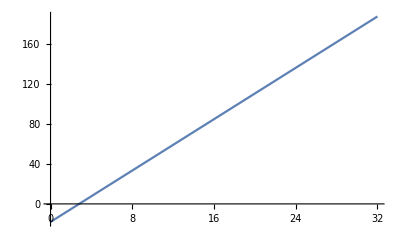

```mathematica
forFit=data⟦2;;,{5,10}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ListPlot[data⟦2;;,{4,3}⟧,
GridLines->{grids@2.5,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,34},{0,34}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

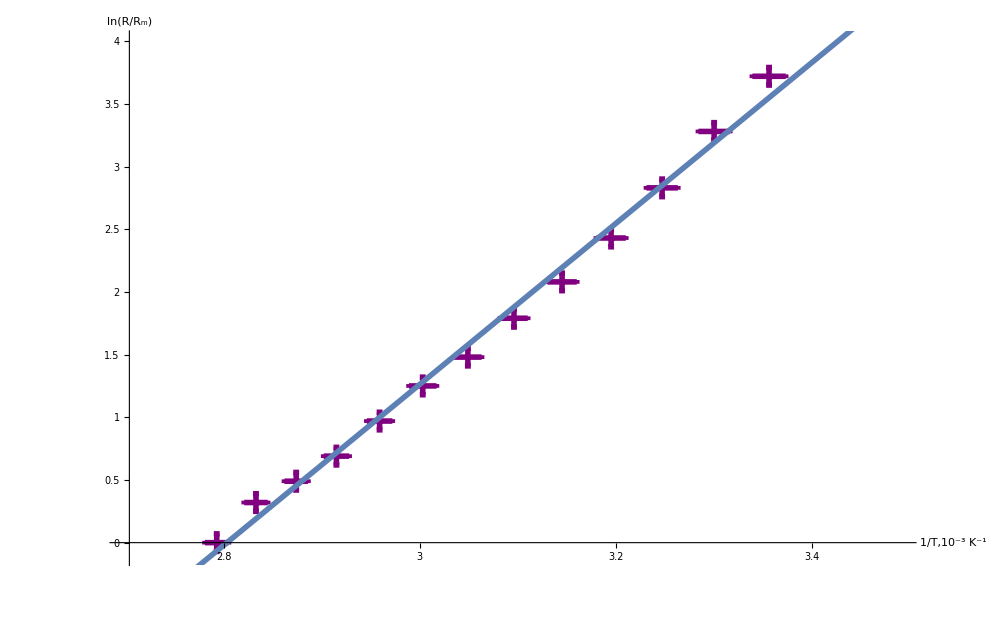

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{5,10,6,11}⟧,
GridLines->{grids@0.05,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/T,10^-3 K^-1","ln(R/R_m)"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX,myTicY},
PlotRange->{{2.7,3.49},{-0.1,4}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,dataT,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{ccccccccc}
 \unicode{2116} & \text{dU, mV} & \text{Rm, Om} & \text{T, K} & \text{1/T, 10${}^{\wedge}$-3 K-1} & \text{} & \text{R, kOm} & \text{} & \text{} \\
 1 & 0.06 & 331 & 298 & 3.356 & 0.017 & 3.31 & 0.17 & 3.72 \\
 2 & 0.265 & 213 & 303 & 3.3 & 0.016 & 2.13 & 0.11 & 3.28 \\
 3 & 0.47 & 135 & 308 & 3.247 & 0.016 & 1.35 & 0.07 & 2.83 \\
 4 & 0.675 & 91 & 313 & 3.195 & 0.015 & 0.91 & 0.05 & 2.43 \\
 5 & 0.88 & 64 & 318 & 3.145 & 0.015 & 0.64 & 0.03 & 2.08 \\
 6 & 1.085 & 48 & 323 & 3.096 & 0.014 & 0.48 & 0.02 & 1.79 \\
 7 & 1.29 & 35 & 328 & 3.049 & 0.014 & 0.35 & 0.02 & 1.48 \\
 8 & 1.495 & 28 & 333 & 3.003 & 0.014 & 0.28 & 0.01 & 1.25 \\
 9 & 1.7 & 21 & 338 & 2.959 & 0.013 & 0.21 & 0.01 & 0.97 \\
 10 & 1.905 & 16 & 343 & 2.915 & 0.013 & 0.16 & 0.01 & 0.69 \\
 11 & 2.11 & 13 & 348 & 2.874 & 0.012 & 0.13 & 0.01 & 0.49 \\
 12 & 2.315 & 11 & 353 & 2.833 & 0.012 & 0.11 & 0.01 & 0.32 \\
 13 & 2.52 & 8 & 358 & 2.793 & 0.012 & 0.08 & 0 & 0 \\
\end{array}
\right)

```mathematica
dataT=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6113/tables/data.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataT//TableForm
```

№ | dU, mV | Rm, Om | T, K | 1/T, 10^-3 K-1 |  | R, kOm |  | 
1. | 0.06 | 331. | 298. | 3.356 | 0.017 | 3.31 | 0.17 | 3.72
2. | 0.265 | 213. | 303. | 3.3 | 0.016 | 2.13 | 0.11 | 3.28
3. | 0.47 | 135. | 308. | 3.247 | 0.016 | 1.35 | 0.07 | 2.83
4. | 0.675 | 91. | 313. | 3.195 | 0.015 | 0.91 | 0.05 | 2.43
5. | 0.88 | 64. | 318. | 3.145 | 0.015 | 0.64 | 0.03 | 2.08
6. | 1.085 | 48. | 323. | 3.096 | 0.014 | 0.48 | 0.02 | 1.79
7. | 1.29 | 35. | 328. | 3.049 | 0.014 | 0.35 | 0.02 | 1.48
8. | 1.495 | 28. | 333. | 3.003 | 0.014 | 0.28 | 0.01 | 1.25
9. | 1.7 | 21. | 338. | 2.959 | 0.013 | 0.21 | 0.01 | 0.97
10. | 1.905 | 16. | 343. | 2.915 | 0.013 | 0.16 | 0.01 | 0.69
11. | 2.11 | 13. | 348. | 2.874 | 0.012 | 0.13 | 0.01 | 0.49
12. | 2.315 | 11. | 353. | 2.833 | 0.012 | 0.11 | 0.01 | 0.32
13. | 2.52 | 8. | 358. | 2.793 | 0.012 | 0.08 | 0. | 0.

```mathematica
{{1, -18.00477849628954, 0.4641429299275719}, {x, 6.4225354068091045, 0.15148969709754778}}
```

{{1,-18.0048,0.464143},{x,6.42254,0.15149}}

```mathematica
TeXForm[{{1,-18.00477849628954,0.4641429299275719},{x,6.4225354068091045,0.15148969709754778}}]
```

\left(
\begin{array}{ccc}
 1 & -18.0048 & 0.464143 \\
 x & 6.42254 & 0.15149 \\
\end{array}
\right)